```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
results={};
sols={};
δvec=(Table[10^eδ,{eδ,-20,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
δvec=(Table[10^eδ,{eδ,-6,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
δvec={9/10};
(*f0vec=Table[10^eδ,{eδ,-6,-1}]//Reverse;*)
f0vec={10^-1};
For[if0=1,if0≤Length[f0vec],if0+=1,
fixf0results={};
f0=f0vec[[if0]];
For[iδ=1,iδ≤Length[δvec],iδ+=1,
δ=δvec[[iδ]];
ϵ=10^-5;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
(*dfdzAtϵ=-((4 (k-q) (9 k^2 (k-q)-6 ⅇ^(2/3 (1/k+ϵ)^2 λ) k (3 k^2+4 (1+k ϵ)^2 λ)+ⅇ^(4/3 (1/k+ϵ)^2 λ) ϵ (2+(k+q) ϵ) λ (9 k^2+4 (1+k ϵ)^2 λ)))/(36 k^2 (k-q)^2 ϵ-3 ⅇ^(2/3 (1/k+ϵ)^2 λ) k (k-q) (3 k (-1+8 k ϵ-q ϵ)+32 ϵ (1+k ϵ)^2 λ)+ⅇ^(4/3 (1/k+ϵ)^2 λ) (9 k^3 (-1+4 k ϵ-q ϵ)+12 k (-1+ϵ (-q+k (3+ϵ (8 k^2 ϵ+k (15-q ϵ)-q (8+3 q ϵ))))) λ+16 ϵ (1+2 k ϵ-q ϵ) (3+2 k ϵ+q ϵ) (λ+k ϵ λ)^2)));*)
(*//.{z->ϵ,ϕ[ϵ]->ic1[[2]],ϕ'[ϵ]->ic2[[2]],G[ϵ]->ic3[[2]],G'[ϵ]->ic4[[2]]}*)
(*Print[StringForm["Check: ``,``",1-δ,ϵ dfdzAtϵ//N]];*)
ic5=f[ϵ]==1+0ϵ dfdzAtϵ;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
fExact[z_]:=1;
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->25,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
sol=First[{ϕ,G,f,β}/.First[tmp]];
(*sol={ϕ,G,f,β}/.ParametricNDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,3/k},{q},AccuracyGoal->∞,WorkingPrecision->25,MaxSteps->∞];*)
{zmin,zmax}=First[sol[[1]]["Domain"]];
zH=tmp[[2,1,1]];
A[z_]:=NIntegrate[(sol[[4]][zp])/(q zp+1),{zp,ϵ,z},MaxRecursion->1000000,Method->{"GlobalAdaptive",MaxErrorIncreases->10000},WorkingPrecision->25];
coeff=Exp[-3A[zH]];
(*Print[StringForm["coeff=``",coeff]];*)
(*Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff}];*)
tmp=NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6,f[Rationalize[zH,0]]==f0},{ϕ,G,f,β},{z,ϵ,Rationalize[zH,0]}];
altsol={ϕ,G,f,β}/.First[tmp];
zHImproved=z/.FindRoot[altsol[[3]][z]==0,{z,zH},WorkingPrecision->25]//Quiet;
AppendTo[sols,altsol[[3]]];
Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff,zHImproved,k zHImproved,-1/(4π)altsol[[3]]'[zHImproved]//Quiet,Exp[-3A[zHImproved]]}];
tmp=NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6,f[Rationalize[zH,0]]==f0},{ϕ,G,f,β},{z,ϵ,Rationalize[zH,0]},WorkingPrecision->25,Method->{"Projection",Method->"ExplicitRungeKutta","Invariants"->{ϕ[z]-G[z]^2/(6 √6)+1}}];
altsol={ϕ,G,f,β}/.First[tmp];
zHImproved=z/.FindRoot[altsol[[3]][z]==0,{z,zH},WorkingPrecision->25]//Quiet;
Print[{"Symplectic",1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff,zHImproved,k zHImproved,-1/(4π)altsol[[3]]'[zHImproved]//Quiet,Exp[-3A[zHImproved]]}];
AppendTo[fixf0results,{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],coeff,k zHImproved,-1/(4π)altsol[[3]]'[zHImproved]//Quiet,Exp[-3A[zHImproved]]}]];
AppendTo[results,fixf0results]]
Show[Table[Plot[sols[[i]][z],{z,ϵ,k^-1 results[[1,i,6]]},PlotStyle->Hue[Rescale[i,{1,Length[sols]}]],PlotRange->All],{i,Length[sols]}]];
Show[Table[Plot[sols[[i]]'[z],{z,ϵ,k^-1 results[[1,i,6]]},PlotStyle->Hue[Rescale[i,{1,Length[sols]}]],PlotRange->All],{i,Length[sols]}]];
Plot[{sol[[1]][z],(sol[[2]][z])^2/(6 √6)}//Evaluate,{z,ϵ,zHImproved}]
Plot[(sol[[1]][z]-(sol[[2]][z])^2/(6 √6))/(√((sol[[1]][z])^2+(sol[[2]][z])^4/216))//Evaluate,{z,ϵ,zHImproved}]
Plot[{(2D[sol[[2]][z](sol[[1]][z]-(sol[[2]][z])^2/(6 √6)),z])/D[sol[[2]][z](sol[[1]][z]+(sol[[2]][z])^2/(6 √6)),z],(2D[altsol[[2]][z](altsol[[1]][z]-(altsol[[2]][z])^2/(6 √6)),z])/D[altsol[[2]][z](altsol[[1]][z]+(altsol[[2]][z])^2/(6 √6)),z]}//Evaluate,{z,ϵ,zHImproved}]
(*ListLinePlot[{results[[1,;;,{1,3}]],results[[1,;;,{1,6}]]},PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]}]
ListLinePlot[{results[[1,;;,{1,4}]],results[[1,;;,{1,7}]]},PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]}]
ListLinePlot[{results[[1,;;,{1,5}]],results[[1,;;,{1,8}]]},PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]}]
ListLinePlot[{results[[1,;;,{4,5}]],results[[1,;;,{7,8}]]},PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]}]*)
```

NDSolve::ndsz: At z == 0.0001757034382546305292435213, step size is effectively zero; singularity or stiff system suspected.

{1/10,0.0001630182500324824226648344,0.1288911211212198752749744,614.1909811280187608892,0.5553478116235463348422571,0.0001756671745713164016737172,0.1388920508604556124729521,643.957,0.418868855343323326840125}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at z == 0.00001.

ReplaceAll::reps: RowBox[{"{", RowBox[{RowBox[{\(\(\(-12\)\ \(f[z]\)\ \(β[z]\)\^2\) + \(3\ \((1 + \(15813091\ z\)\/200000)\)\ \((\(\(β[z]\)\ \(\(\*SuperscriptBox["f", "′", Rule[MultilineFunction, None]]\)[z]\)\) + \(\(f[z]\)\ \((\(\(\*SuperscriptBox[\(« 1 »\), TagBox[\((\(« 1 »\))\), Derivative], Rule[MultilineFunction, None]]\)[\(« 1 »\)]\) + \(Times[\(« 3 »\)]\))\)\))\)\)\), "==", RowBox[{\(-\(\(750161540922843\ ⅇ\^\(\(-\@\(« 1 »\)\)\ \(« 1 »\)\)\)\/100000000\)\), "-", FractionBox[\(« 1 »\), RowBox[{"", \(« 8 »\), ""}]], "-", \(« 1 »\), "+", \(18\ \((\(250053846974281\ \(« 1 »\)\)\/14400000000 + \((\(« 1 »\))\)\^2)\)\)}]}], ",", \(« 8 »\), ",", \(« 1 »\)}], "}"}] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

ReplaceAll::reps: -12 f[0.0001630182500324824226648343761188138989543240689683272904`25.] β[0.0001630182500324824226648343761188138989543240689683272904`25.]^2 + « 79 » (β[« 64 »] SuperscriptBox[« 8 »« 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

FindRoot::nlnum: The function value {({ϕ, G, f, β}/. {« 1 »}) ⟦ 3 ⟧[0.0001630182500324824226648344]} is not a list of numbers with dimensions {1} at {z} = {0.0001630182500324824226648344}.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {({ϕ, G, f, β}/. {« 1 »}) ⟦ 3 ⟧[0.0001630182500324824226648344]} is not a list of numbers with dimensions {1} at {z} = {0.0001630182500324824226648344}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

NIntegrate::nlim: zp = z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25.] is not a valid limit of integration.

{Symplectic,1/10,0.0001630182500324824226648344,0.1288911211212198752749744,614.1909811280187608892,0.5553478116235463348422571,z/.FindRoot[altsol⟦3⟧[z]==0,{z,zH},WorkingPrecision→25],(15813091 (z/.FindRoot[altsol⟦3⟧[z]==0,{z,zH},WorkingPrecision→25]))/20000,-1/(4 π)({ϕ,G,f,β}/.{-12 f[z] β[z]^2+3 (1+(15813091 z)/200000) (β[z] f'[z]+f[z] (β'[z]+(β[z] ϕ'[z])/(√6)))==-(750161540922843 ⅇ^(-√(2/3) ϕ[z]))/100000000-(750161540922843 ⅇ^(-ϕ[z]/(√6)) (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6)))/50000000-(750161540922843 (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6))^2)/100000000+18 ((250053846974281 G[z]^2)/14400000000+((15813091 (-1/(√6)+ⅇ^(-ϕ[z]/(√6))/(√6)))/20000+(15813091 (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6)))/(20000 √6))^2),6 (β'[z]+(β[z] ϕ'[z])/(√6))==(1+(15813091 z)/200000) (G'[z]^2+ϕ'[z]^2),(1+(15813091 z)/200000) f'[z] ϕ'[z]+f[z] ((15813091/200000-4 β[z]) ϕ'[z]+((1+(15813091 z)/200000) ϕ'[z]^2)/(√6)+(1+(15813091 z)/200000) ϕ''[z])==((250053846974281 √(3/2) (2-2 ⅇ^(-√(2/3) ϕ[z])-3/2 (-1/12 G[z]^2+ϕ[z]/(√6))))/100000000+√(2/3) (-(750161540922843 ⅇ^(-ϕ[z]/(√6)) (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6)))/50000000-(750161540922843 (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6))^2)/100000000+18 ((250053846974281 G[z]^2)/14400000000+((15813091 (-1/(√6)+ⅇ^(-ϕ[z]/(√6))/(√6)))/20000+(15813091 (1-ⅇ^(-ϕ[z]/(√6))+G[z]^2/12-ϕ[z]/(√6)))/(20000 √6))^2)))/(1+(15813091 z)/200000),(1+(15813091 z)/200000) f'[z] G'[z]+f[z] ((15813091/200000-4 β[z]) G'[z]+((1+(15813091 z)/200000) G'[z] ϕ'[z])/(√6)+(1+(15813091 z)/200000) G''[z])==-(250053846974281 G[z] (3/2-3/2 (-1/12 G[z]^2+ϕ[z]/(√6))))/(200000000 (1+(15813091 z)/200000)),ϕ[1/100000]==(1354500805948991427 √(3/2))/1533386890000000000,ϕ'[1/100000]==(858064439069 √(3/2))/619150000,G[1/100000]==(2015813091 √(3/2))/619150000,G'[1/100000]==1277 √6,β[1/100000]==(15813091 ⅇ^(-ϕ[1/100000]/(√6)))/200000+(15813091 (1-ⅇ^(-ϕ[1/100000]/(√6))+1/12 G[1/100000]^2-ϕ[1/100000]/(√6)))/20000,f[48090946879/295003454333595]==1/10})⟦3⟧'[z/.FindRoot[altsol⟦3⟧[z]==0,{z,zH},WorkingPrecision→25]],ⅇ^(-3 NIntegrate[(sol⟦4⟧[zp])/(q zp+1),{zp,ϵ,z/.FindRoot[altsol⟦3⟧[z]==0,{z,zH},WorkingPrecision→25]},MaxRecursion→1000000,Method→{GlobalAdaptive,MaxErrorIncreases→10000},WorkingPrecision→25])}

NIntegrate::nlim: zp = z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25.] is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

ReplaceAll::reps: RowBox[{"{", RowBox[{RowBox[{\(\(\(-12\)\ \(f[z]\)\ \(β[z]\)\^2\) + \(3\ \((1 + \(15813091\ z\)\/200000)\)\ \((\(\(β[z]\)\ \(\(\*SuperscriptBox["f", "′", Rule[MultilineFunction, None]]\)[z]\)\) + \(\(f[z]\)\ \((\(\(\*SuperscriptBox[\(« 1 »\), TagBox[\((\(« 1 »\))\), Derivative], Rule[MultilineFunction, None]]\)[\(« 1 »\)]\) + \(Times[\(« 3 »\)]\))\)\))\)\)\), "==", RowBox[{\(-\(\(750161540922843\ ⅇ\^\(\(-\@\(« 1 »\)\)\ \(« 1 »\)\)\)\/100000000\)\), "-", FractionBox[\(« 1 »\), RowBox[{"", \(« 8 »\), ""}]], "-", \(« 1 »\), "+", \(18\ \((\(250053846974281\ \(« 1 »\)\)\/14400000000 + \((\(« 1 »\))\)\^2)\)\)}]}], ",", \(« 8 »\), ",", \(« 1 »\)}], "}"}] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

ReplaceAll::reps: -12 f[0.0001630182500324824226648343761188138989543240689683272904`25.] β[0.0001630182500324824226648343761188138989543240689683272904`25.]^2 + « 79 » (β[« 64 »] SuperscriptBox[« 8 »« 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

ReplaceAll::reps: {-12.\ f[0.0001630182500324824226648344]\ β[0.0001630182500324824226648344]^2 + « 64 »\ (β[« 64 »]\ « 1 » + « 1 ») == « 1 », « 8 », « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 3 of {ϕ, G, f, β} « 2 »  {-12.\ f[0.0001630182500324824226648344]\ β[0.0001630182500324824226648344]^2 + « 64 »\ (« 1 ») == « 1 », « 8 », « 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

FindRoot::nlnum: The function value {({ϕ, G, f, β}/. {« 1 »}) ⟦ 3 ⟧[0.0001630182500324824226648344]} is not a list of numbers with dimensions {1} at {z} = {0.0001630182500324824226648344}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

NIntegrate::nlim: zp = z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25.] is not a valid limit of integration.

FindRoot::precw: The precision of the argument function (({ϕ, G, f, β}/. {« 1 »}) ⟦ 3 ⟧[z] == 0.) is less than WorkingPrecision (25.).

Plot::plln: Limiting value z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25] in {z, ϵ, results ⟦ 1, i, 6 ⟧/k} is not a machine-sized real number.

NIntegrate::nlim: zp = z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25.] is not a valid limit of integration.

FindRoot::precw: The precision of the argument function (({ϕ, G, f, β}/. {« 1 »}) ⟦ 3 ⟧[z] == 0.) is less than WorkingPrecision (25.).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

Plot::plln: Limiting value z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25] in {z, ϵ, results ⟦ 1, i, 6 ⟧/k} is not a machine-sized real number.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

NIntegrate::nlim: zp = z/. FindRoot[altsol ⟦ 3 ⟧[z] == 0, {z, zH}, WorkingPrecision → 25.] is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::precw: The precision of the argument function (TagBox[InterpolatingFunction[{{1.`25.*^-5, « 64 »}}, « 3 », {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][zp]) is less than WorkingPrecision (25.).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

$Aborted

ReplaceAll::reps: RowBox[{"{", RowBox[{RowBox[{\(\(\(-12\)\ \(f[z]\)\ \(β[z]\)\^2\) + \(3\ \((1 + \(15813091\ z\)\/200000)\)\ \((\(\(β[z]\)\ \(\(\*SuperscriptBox["f", "′", Rule[MultilineFunction, None]]\)[z]\)\) + \(\(f[z]\)\ \((\(\(\*SuperscriptBox[\(« 1 »\), TagBox[\((\(« 1 »\))\), Derivative], Rule[MultilineFunction, None]]\)[\(« 1 »\)]\) + \(Times[\(« 3 »\)]\))\)\))\)\)\), "==", RowBox[{\(-\(\(750161540922843\ ⅇ\^\(\(-\@\(« 1 »\)\)\ \(« 1 »\)\)\)\/100000000\)\), "-", FractionBox[\(« 1 »\), RowBox[{"", \(« 8 »\), ""}]], "-", \(« 1 »\), "+", \(18\ \((\(250053846974281\ \(« 1 »\)\)\/14400000000 + \((\(« 1 »\))\)\^2)\)\)}]}], ",", \(« 8 »\), ",", \(« 1 »\)}], "}"}] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

ReplaceAll::reps: -12 f[0.0001630182500324824226648343761188138989543240689683272904`25.] β[0.0001630182500324824226648343761188138989543240689683272904`25.]^2 + « 79 » (β[« 64 »] SuperscriptBox[« 8 »« 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {ϕ, G, f, β}/. {« 1 »} does not exist.

ReplaceAll::reps: {-12.\ f[0.0001630182500324824226648344]\ β[0.0001630182500324824226648344]^2 + « 64 »\ (β[« 64 »]\ « 1 » + « 1 ») == « 1 », « 8 », « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

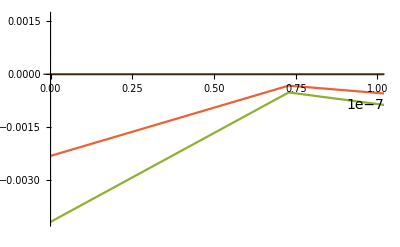

```mathematica
tmpPlot=Module[{ϕ,G,f,β},
ϕ[z_]:=altsol[[1]][z];
G[z_]:=altsol[[2]][z];
f[z_]:=altsol[[3]][z];
β[z_]:=altsol[[4]][z];
eqn1LHS=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2;
eqn1RHS=ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2LHS=6(a ϕ'[z]β[z]+β'[z]);
eqn2RHS=(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3LHS=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z];
eqn3RHS=1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4LHS=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z];
eqn4RHS=1/(q z+1)dςdG[ϕ[z],G[z]];
Plot[{2(eqn1LHS-eqn1RHS)/(eqn1LHS+eqn1RHS),2(eqn2LHS-eqn2RHS)/(eqn2LHS+eqn2RHS),2(eqn3LHS-eqn3RHS)/(eqn3LHS+eqn3RHS),2(eqn4LHS-eqn4RHS)/(eqn4LHS+eqn4RHS)}//Evaluate,{z,ϵ,zH},PlotRange->{{0,10^-7},All}]];
tmpPlot
```

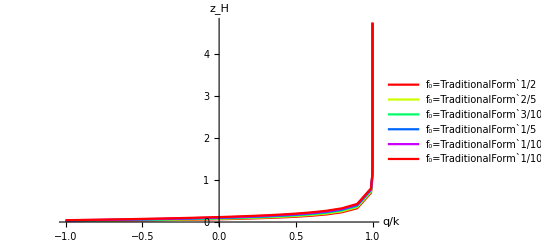

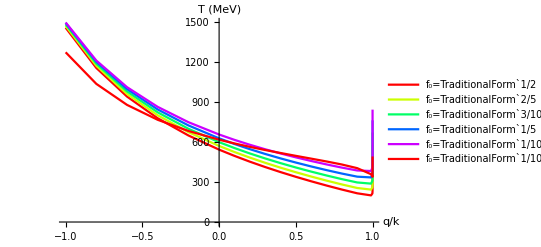

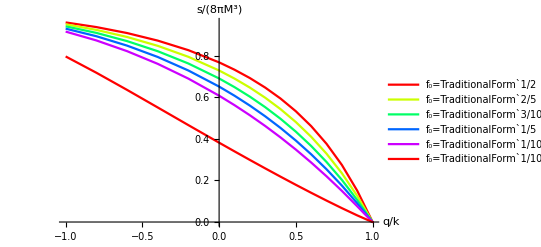

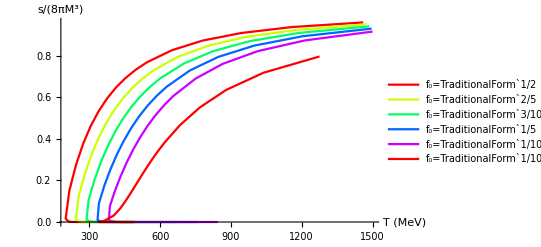

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
plotLegends=Table[StringForm["f_0=``",f0vec[[i]]],{i,Length[results]}];
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{4,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
dΩdϕ[ϕ_,G_]:=(-a+a ⅇ^(-a ϕ)) k;
dΩdG[ϕ_,G_]:=k U'[G];
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+dΩdϕ[ϕ,G])^2+(dΩdG[ϕ,G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
ϕ[z_]:=G[z]^2/(6 √6);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
eqn1//FullSimplify
eqn2//FullSimplify
eqn3//FullSimplify
eqn4//FullSimplify
```

1/36 k^2 (432+30 G[z]^2+G[z]^4)+3 (1+q z) (β[z] (f'[z]+1/18 f[z] G[z] G'[z])+f[z] β'[z])==12 f[z] β[z]^2

G'[z] (-18 G[z] β[z]+(1+q z) (54+G[z]^2) G'[z])==324 β'[z]

1/(1+q z)(3 k^2 G[z]^4+18 (1+q z)^2 f[z] G'[z]^2+G[z]^2 (36 k^2+(1+q z)^2 f[z] G'[z]^2)+18 (1+q z) G[z] ((f[z] (q-4 β[z])+(1+q z) f'[z]) G'[z]+(1+q z) f[z] G''[z]))==0

(k^2 G[z] (18+G[z]^2))/(6+6 q z)+(1+q z) f'[z] G'[z]+f[z] ((q-4 β[z]) G'[z]+1/18 (1+q z) G[z] G'[z]^2+(1+q z) G''[z])==0